```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
tMin=-1/10;
```

```mathematica
(* n = -1 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
sol =NDSolve[{Y'[t] == v[t], v'[t] == 2*Cxi[1/10]*(Y[t])^(-1), Y[ti]==1,v[ti]==2*Hti,WhenEvent[Y[t]==0,"StopIntegration","LocationMethod"->"Brent"]},{Y,v},{t,tMin,ti},WorkingPrecision->40,AccuracyGoal->25,PrecisionGoal->25,MaxStepFraction->1/1000,MaxSteps->Infinity];
```

```mathematica
apos[t_]:=ai*Sqrt[Y[t]/. sol[[1]]];
aneg[t_]:=-ai*Sqrt[Y[t]/. sol[[1]]];
```

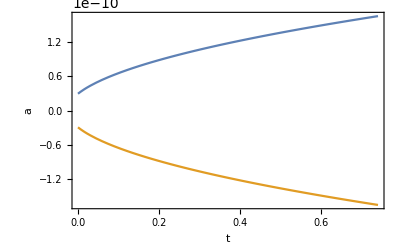

```mathematica
Plot[{apos[t],aneg[t]}, {t, 0, ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

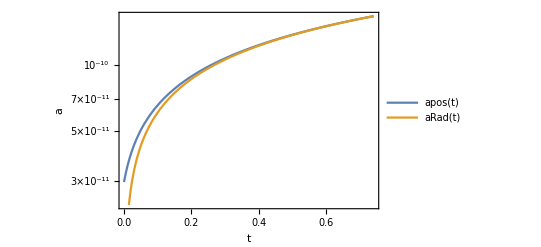

```mathematica
LogPlot[{apos[t], aRad[t]}, {t, 0, ti}, PlotLegends->"Expressions", AxesLabel->{t,a}, Frame->True, PlotRangePadding->0]
```